## Struck Twice By Lightning: Steven Pinker’s Problem

Suppose you live in a place that has a constant chance of being struck by lightning at any time throughout the year. Suppose the strikes are random: every day the chance of a strike is the same and the rate works out to be one strike a month. Your house is hit by lightning today, Monday. What is the most likely day for the next bolt of lightning to strike your house?

## Approach

Since the probability of a strike is 12/365 (strike rate = once a month), model this phenomenon as a series of 1s and 0s with the probability of 1s set at 12/365. Call this the trial generator.
A trial is a string of 365 ones and zeroes generated by the trial generator. For each trial, the relevant pattern is a string of two consecutive 1s. How many of these are generated in a trial? The frequency of these consecutive events is this number divided by 364 -- that’s the number of comparisons between each of the two tuples in the string.
NOTE: Of course we could have used a Poisson process and did this all in a much faster way. But I wanted to keep things as close to the ground as possible and roll everything from scratch. If we “discovered” some results about Poisson or Binomial processes, then that’s a bonus. (That’s just the perspective I’ve adopted for this investigation.)

## Trial Generator

Trial generator g

```mathematica
trialLength = 365;
pStrike = N[12/365];
pBlank = 1 - pStrike;
(* The Trial *)
trial = RandomChoice[{pStrike, pBlank}->{1,0},trialLength]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Now generate a slew of trials *)
nTrials = 1000;
setOfTrials = Table[RandomChoice[{pStrike, pBlank}->{1,0},trialLength],{nTrials}];
```

```mathematica
(* Test if each of the trials is distinct *)
setOfTrials[[1]] == setOfTrials[[2]];
```

## Two Patterns We Care About to Solve Pinker’s Problem

Pattern 1: Each occurrence of 1 in the trial that is followed immediately by a 1. We’d like to know the number of these occurrences in the trial -- p1Count.
Pattern 2: Each occurrence of a 1 in the trial that is followed immediately by a 0. We’d like to know the number of these occurrences in the trial -- p2Count.

```mathematica
(* Partition the trial into 2-tuples to check for the patterns below *)
t = Partition[trial, 2,1];
(* Total number of 2-tuples in t *)
tLength = Length[t]
(* Pattern 1 to check for *)
p1 = {1,1};
(* Pattern 2 to check for *)
p2 = {1,0};
```

364

```mathematica
(* Number of times pattern 1 occurs in a trial *)
p1Count = Count[t,p1]
```

1

```mathematica
(* Frequency with which pattern 1 occurs in a trial *)
p1Freq = N[p1Count/tLength]
```

0.00274725

```mathematica
(* Number of times pattern 2 occurs in a trial *)
p2Count = Count[t,p2]
```

6

```mathematica
(* Frequency with which pattern 2 occurs in a trial *)
p2Freq = N[p2Count/tLength]
```

0.0164835

```mathematica
(* Create the function that will calculate the frequencies for a single trial *)
(* Patterns are always in the form of 2-tuples which can be of any length *)
patternFrequency[trial_,pattern_]:= Module[{t,tLength, pCount, pFreq},
(* Partition the trial into 2-tuples to check for the patterns below *)
t = Partition[trial, 2,1];
(* Total number of 2-tuples in t *)
tLength = Length[t];
(* Number of times the pattern occurs in a trial *)
pCount = Count[t,pattern];
(* Frequency with which the pattern occurs in a trial *)
pFreq = N[pCount/tLength]
];
```

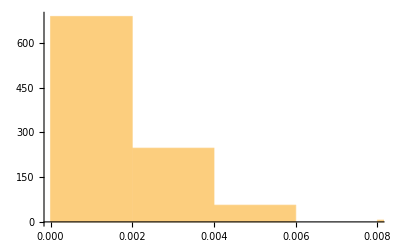

```mathematica
(* Distribution of occurrences of a 1 followed immediately by another 1 *)
p1Frequency = Histogram[patternFrequency[#,{1,1}] & /@ setOfTrials]
```

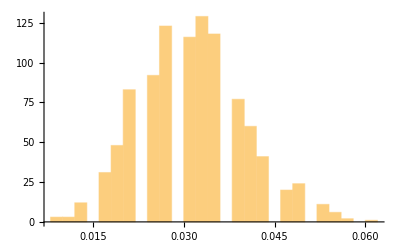

```mathematica
(* Distribution of occurrences of a 1 followed immediately by another 0 *)
p2Frequency = Histogram[patternFrequency[#,{1,0}] & /@ setOfTrials]
```

Comparing these two histograms we see that for a randomly generated sequence of 365 1s and 0s, the probability of a 1 followed by a 0 is about 10 times that of the probabilty of a 1 followed by a 1.
It’s not clear why the frequency of a 1 followed by a 0 (the above histogram) is gappy. Have we discovered something through the simulation?

## A More General Pattern Matcher

```mathematica
(* Create a more general pattern matching function that will detect patterns that are of any length *)
patternFrequency2[trial_,pattern_]:= Module[{partLength, partOffset,t,tLength, pCount, pFreq},
(* First figure out the length of the partition based on the length of the pattern *)
partLength = Length[pattern];
(* The offset for the tuples is partLength - 1 *)
partOffset = partLength -1;
(* Partition the trial into 2-tuples to check for the patterns below *)
t = Partition[trial, partLength,partOffset];
(* Total number of 2-tuples in t *)
tLength = Length[t];
(* Number of times the pattern occurs in a trial *)
pCount = Count[t,pattern];
(* Frequency with which the pattern occurs in a trial *)
pFreq = N[pCount/tLength]
];
```

```mathematica
patternFrequency2[#,{1,0,1}] & /@ setOfTrials;
```

So far we have shown that a 1 followed by another 1 is NOT the most probable pattern. But what IS the most probable pattern? Is that even a well posed question? Let’s find out.

## The Distance Between Strikes

We know that it’s very rare for a strike to be followed immediately by a strike. What is the “distance” between strikes in a trial? Let’s look at this question.

```mathematica
(* Distance between strikes in a trial is the distance between the 1s that occur in a trial. *)
pos = Flatten[Position[trial,1]]
```

{50,80,127,128,223,241,246}

```mathematica
(* Create 2-tuples of the pos values so that they can be subtracted to find the distance -- or the number of blanks -- between strikes. *)
distance = Partition[pos,2,1] /. {x_,y_} -> Subtract[y,x]
```

{30,47,1,95,18,5}

```mathematica
(* Create the function for distance between strikes *)
strikeDistance[trial_]:= Module[{pos,distance},
(* Distance between strikes in a trial is the distance between the 1s that occur in a trial. *)
pos = Flatten[Position[trial,1]];
(* Create 2-tuples of the pos values so that they can be subtracted to find the distance -- or the number of blanks -- between strikes. *)
distance = Partition[pos,2,1] /. {x_,y_} -> Subtract[y,x]
];
```

```mathematica
(* Now we can calculate the distance between strikes over the set of all trials. *)
sd = strikeDistance[#] & /@ setOfTrials;
```

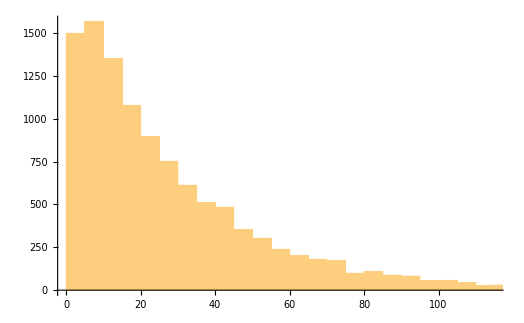

```mathematica
(* Represent this as a single histogram *)
hsd = Histogram[Flatten[sd]]
```

Notice how the distance between strikes drops off exponentially. As Pinker puts it on page 203 of his book The Better Angels of Our Nature, “[I]n a Poisson process the intervals between events are distributed exponentially: there are lots of short intervals and fewer and fewer of them as they get longer and longer.” Exactly.
However, notice that the most common distance between strikes is between 5 and 10 days. It’s interesting to see that the frequency of strikes between 0 and 5 days is the second highest frequency in the histogram. This seems even more counterproductive than Pinker’s claim that the most probable distance between events is 1 day!

## A Simple and General Strike Pattern Calculator

It is easier to detect patterns of strikes and blanks if we just focus on the distance between strikes. A distance of 1 means two strikes occur in sequential order. A distance of 2 between strikes means that a blank occurs between 2 strikes, and so on.
Using this method we can calculate the frequency of any particular string of 1*1 -- that is a 1 followed by a certain number of zeroes and then a 1 again.

```mathematica
(* Create the function for distance between strikes *)
strikeDistance2[trial_,dist_]:= Module[{pos,distances, d},
(* Distance between strikes in a trial is the distance between the 1s that occur in a trial. *)
pos = Flatten[Position[trial,1]];
(* Create 2-tuples of the pos values so that they can be subtracted to find the distance -- or the number of blanks -- between strikes. *)
distances = Partition[pos,2,1] /. {x_,y_} -> Subtract[y,x];
(* The number of instances where the distance = dist *)
d = Count[distances,dist]
];
```

```mathematica
(* For any distance from 1 to 364, does this distance occur in a single trial? If yes, the series below will have a 1 -- if not, a 0. *)
strikeDistance2[trial, #] & /@ Range[364]
```

{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Now we can ask the question we need to ask to see if Pinker’s solution is correct. The question is: Over a set of trials, say 1000 trials, does a distance of 1 occur more frequently than any other distance? Let’s see.

```mathematica
(* The number of occurrences of distance = 1, 2, 3, ...,364 over the set of trials normalized by the number of trials *)
distFrequency = Table[Total@(strikeDistance2[#, i] & /@ setOfTrials), {i,1,trialLength-1}]
```

{391,380,390,336,343,294,312,313,304,278,256,284,256,274,225,231,214,208,199,171,172,185,170,196,146,145,158,154,149,142,134,123,114,99,90,119,103,93,104,106,102,93,91,92,82,66,58,71,75,68,60,58,56,61,47,40,50,53,49,47,40,39,41,35,41,34,22,41,42,37,34,29,45,26,21,12,28,20,18,25,22,19,22,19,18,17,23,14,16,19,18,12,16,17,12,15,11,12,6,14,13,11,13,6,6,12,9,5,12,7,5,4,4,5,11,4,6,3,6,1,3,5,2,5,6,4,3,3,1,5,3,3,4,5,2,2,3,3,1,2,3,2,0,3,3,0,1,2,2,1,4,3,2,4,1,0,1,3,1,0,1,2,1,2,1,0,2,1,0,2,0,1,1,0,2,0,0,0,2,1,0,1,0,1,1,0,1,1,0,0,1,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
distFrequencyTotal = Total@distFrequency
```

10912

```mathematica
distFrequencyNormalized = distFrequency/distFrequencyTotal //N
```

{0.0358321,0.034824,0.0357405,0.0307918,0.0314333,0.0269428,0.0285924,0.028684,0.0278592,0.0254765,0.0234604,0.0260264,0.0234604,0.02511,0.0206195,0.0211694,0.0196114,0.0190616,0.0182368,0.0156708,0.0157625,0.0169538,0.0155792,0.0179619,0.0133798,0.0132881,0.0144795,0.0141129,0.0136547,0.0130132,0.0122801,0.011272,0.0104472,0.00907258,0.0082478,0.0109054,0.00943915,0.00852273,0.00953079,0.00971408,0.00934751,0.00852273,0.00833944,0.00843109,0.00751466,0.00604839,0.00531525,0.0065066,0.00687317,0.00623167,0.00549853,0.00531525,0.00513196,0.00559018,0.00430718,0.00366569,0.00458211,0.00485704,0.00449047,0.00430718,0.00366569,0.00357405,0.00375733,0.00320748,0.00375733,0.00311584,0.00201613,0.00375733,0.00384897,0.00339076,0.00311584,0.00265762,0.0041239,0.0023827,0.00192449,0.00109971,0.00256598,0.00183284,0.00164956,0.00229106,0.00201613,0.0017412,0.00201613,0.0017412,0.00164956,0.00155792,0.00210777,0.00128299,0.00146628,0.0017412,0.00164956,0.00109971,0.00146628,0.00155792,0.00109971,0.00137463,0.00100806,0.00109971,0.000549853,0.00128299,0.00119135,0.00100806,0.00119135,0.000549853,0.000549853,0.00109971,0.00082478,0.000458211,0.00109971,0.000641496,0.000458211,0.000366569,0.000366569,0.000458211,0.00100806,0.000366569,0.000549853,0.000274927,0.000549853,0.0000916422,0.000274927,0.000458211,0.000183284,0.000458211,0.000549853,0.000366569,0.000274927,0.000274927,0.0000916422,0.000458211,0.000274927,0.000274927,0.000366569,0.000458211,0.000183284,0.000183284,0.000274927,0.000274927,0.0000916422,0.000183284,0.000274927,0.000183284,0.,0.000274927,0.000274927,0.,0.0000916422,0.000183284,0.000183284,0.0000916422,0.000366569,0.000274927,0.000183284,0.000366569,0.0000916422,0.,0.0000916422,0.000274927,0.0000916422,0.,0.0000916422,0.000183284,0.0000916422,0.000183284,0.0000916422,0.,0.000183284,0.0000916422,0.,0.000183284,0.,0.0000916422,0.0000916422,0.,0.000183284,0.,0.,0.,0.000183284,0.0000916422,0.,0.0000916422,0.,0.0000916422,0.0000916422,0.,0.0000916422,0.0000916422,0.,0.,0.0000916422,0.000183284,0.0000916422,0.0000916422,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000183284,0.,0.,0.,0.,0.000183284,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000916422,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000916422,0.,0.0000916422,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

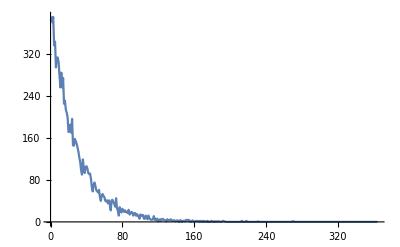

```mathematica
(* Plot the result in a simple list plot *)
pdistFrequency = ListLinePlot[distFrequency, PlotRange->All]
```

We see that Pinker is right! What a counterintuitive result! One of the most counterintuitive things about this result is that the probability (or, strictly speaking, the frequency of occurrence) of distance = 1 is not that much higher than the frequency of occurrence of distance = 2 or distance = 3. But after that, the drop off in probability of the larger distances is pretty steep!

## Putting It All Together

All It Putting Together

Now we’ll put it all together. How sensitive is the result to the probability of a strike, the length of a single trial, and the number of trials in the set of all trials?

```mathematica
(* Create a function for calculating and manipulating strike distance. Normalize the counts for each distance so we can compare them no matter how many trials we choose. *)
distanceCalculator[probStrike_, trialLength_, nTrials_]:= Module[{probBlank, trial, setOfTrials, distFrequency, distFrequencyTotal,distFrequencyNormalized,pdistFrequencyNormalized},
probBlank = 1 - probStrike;
(* The single trial *)
trial = RandomChoice[{probStrike, probBlank}->{1,0},trialLength];
(* The set of trials *)
setOfTrials = Table[RandomChoice[{probStrike, probBlank}->{1,0},trialLength],{nTrials}];
(* So up to now we have the variables of the function determining the nature of the trial and the set of trials. *)
(* Now calculate the distribution frequency *)
distFrequency = Table[Total@(strikeDistance2[#, i] & /@ setOfTrials), {i,1,trialLength-1}];
(* Normalize the distFrequency so that it can be expressed as a probability *)
distFrequencyTotal = Total@distFrequency;
(* The Quiet ensures that dividing by 0 -- which happens if the probStrike is very low -- does not trigger an error message. *)
distFrequencyNormalized = Quiet[distFrequency/distFrequencyTotal] //N;
(* Plot the result in a simple list plot *)
pdistFrequencyNormalized = ListLinePlot[distFrequencyNormalized, PlotRange->{{1,50},All}, AxesOrigin-> {1,0}];
(* distFrequencyNormalized *)
(* pdistFrequencyNormalized *)
distFrequency/nTrials //N
];
```

```mathematica
(* The number of times the strike distance occurs per trial *)
distanceCalculator[0.04,100,1000]
```

{0.154,0.138,0.15,0.126,0.123,0.136,0.112,0.099,0.125,0.096,0.102,0.107,0.09,0.062,0.068,0.069,0.078,0.053,0.058,0.069,0.041,0.055,0.049,0.041,0.048,0.036,0.033,0.043,0.039,0.047,0.035,0.037,0.03,0.028,0.028,0.023,0.023,0.024,0.027,0.017,0.018,0.018,0.013,0.017,0.012,0.012,0.014,0.017,0.014,0.012,0.013,0.006,0.003,0.006,0.01,0.006,0.005,0.009,0.006,0.005,0.006,0.003,0.004,0.003,0.002,0.001,0.001,0.006,0.004,0.,0.005,0.006,0.001,0.,0.002,0.001,0.002,0.001,0.001,0.001,0.001,0.001,0.002,0.001,0.,0.,0.001,0.001,0.002,0.,0.001,0.001,0.001,0.,0.002,0.001,0.,0.,0.}

{0.14,0.167,0.153,0.164,0.129,0.136,0.12,0.135,0.114,0.09,0.12,0.085,0.092,0.064,0.081,0.094,0.075,0.064,0.072,0.06,0.054,0.051,0.055,0.053,0.047,0.038,0.043,0.03,0.026,0.042,0.024,0.03,0.031,0.018,0.026,0.03,0.024,0.022,0.024,0.024,0.015,0.013,0.017,0.015,0.019,0.017,0.015,0.011,0.005,0.006,0.014,0.007,0.013,0.007,0.008,0.009,0.011,0.004,0.002,0.006,0.006,0.005,0.005,0.007,0.001,0.005,0.002,0.003,0.003,0.001,0.003,0.001,0.001,0.002,0.003,0.003,0.,0.005,0.001,0.003,0.002,0.001,0.,0.002,0.001,0.002,0.001,0.,0.,0.,0.,0.,0.001,0.,0.,0.,0.,0.,0.}

{0.14,0.167,0.153,0.164,0.129,0.136,0.12,0.135,0.114,0.09,0.12,0.085,0.092,0.064,0.081,0.094,0.075,0.064,0.072,0.06,0.054,0.051,0.055,0.053,0.047,0.038,0.043,0.03,0.026,0.042,0.024,0.03,0.031,0.018,0.026,0.03,0.024,0.022,0.024,0.024,0.015,0.013,0.017,0.015,0.019,0.017,0.015,0.011,0.005,0.006,0.014,0.007,0.013,0.007,0.008,0.009,0.011,0.004,0.002,0.006,0.006,0.005,0.005,0.007,0.001,0.005,0.002,0.003,0.003,0.001,0.003,0.001,0.001,0.002,0.003,0.003,0.,0.005,0.001,0.003,0.002,0.001,0.,0.002,0.001,0.002,0.001,0.,0.,0.,0.,0.,0.001,0.,0.,0.,0.,0.,0.}

{0.143,0.143,0.133,0.14,0.13,0.122,0.113,0.12,0.091,0.092,0.081,0.101,0.09,0.08,0.067,0.075,0.075,0.059,0.057,0.064,0.053,0.058,0.057,0.038,0.039,0.04,0.051,0.034,0.033,0.032,0.042,0.018,0.036,0.027,0.017,0.017,0.019,0.023,0.022,0.02,0.024,0.024,0.018,0.018,0.017,0.018,0.016,0.017,0.01,0.01,0.009,0.015,0.008,0.009,0.006,0.008,0.005,0.005,0.009,0.006,0.004,0.003,0.006,0.001,0.,0.005,0.004,0.003,0.002,0.007,0.002,0.002,0.001,0.002,0.003,0.,0.002,0.002,0.002,0.,0.001,0.001,0.001,0.002,0.001,0.,0.,0.001,0.001,0.001,0.,0.001,0.,0.,0.,0.,0.,0.,0.}

{0.143,0.143,0.133,0.14,0.13,0.122,0.113,0.12,0.091,0.092,0.081,0.101,0.09,0.08,0.067,0.075,0.075,0.059,0.057,0.064,0.053,0.058,0.057,0.038,0.039,0.04,0.051,0.034,0.033,0.032,0.042,0.018,0.036,0.027,0.017,0.017,0.019,0.023,0.022,0.02,0.024,0.024,0.018,0.018,0.017,0.018,0.016,0.017,0.01,0.01,0.009,0.015,0.008,0.009,0.006,0.008,0.005,0.005,0.009,0.006,0.004,0.003,0.006,0.001,0.,0.005,0.004,0.003,0.002,0.007,0.002,0.002,0.001,0.002,0.003,0.,0.002,0.002,0.002,0.,0.001,0.001,0.001,0.002,0.001,0.,0.,0.001,0.001,0.001,0.,0.001,0.,0.,0.,0.,0.,0.,0.}

What we’d like to do is clean up the calculation above and be able display the following. For distances 1 through 5, let’s plot the number of occurrences of each distance in each trial. We do this for each trial in the set of trials. This plot will have 5 lines, one for each value of distance from 1 to 5. We can then see from trial to trial, how these lines vary as we change the probability of a strike, the length of each trial and the number of trails we conduct.

```mathematica
(* Create a function for calculating and manipulating the occurences of strike distances as a function of the strike probability, the length of a single trial and the number of trials we conduct (which is defaulted to 500) *)
distanceCalculator2[probStrike_, trialLength_, nTrials_:1000]:= Module[{probBlank, trial, setOfTrials, maxDistance,totalOccurrences, distOccurrencePerTrial, pdistOccurrencePerTrial},
probBlank = 1 - probStrike;
(* Generate the set of nTrials trials *)
setOfTrials = Table[RandomChoice[{probStrike, probBlank}->{1,0},trialLength],{nTrials}];
(* For each distance value, calculate the number of occurrences of that distance value in each trial. *)
(* Only the first few distances are relevant -- so save time and calculate only for those distances. *)
maxDistance = 30;
(* Total count of the occurrences of the distance in the set of trials *)
totalOccurrences = Table[Total@(strikeDistance2[#, i] & /@ setOfTrials), {i,1,maxDistance}];
distOccurrencePerTrial = Table[N[Total@(strikeDistance2[#, i] & /@ setOfTrials)/nTrials], {i,1,maxDistance}];
(* pdistOccurrencePerTrial = ListLinePlot[distOccurrencePerTrial] *)
totalOccurrences
];
```

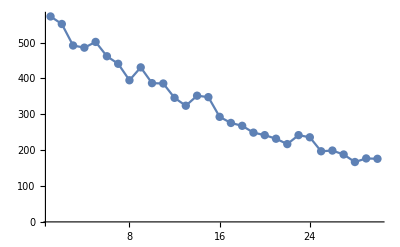
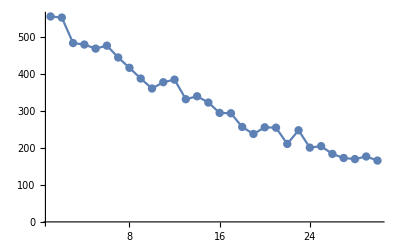
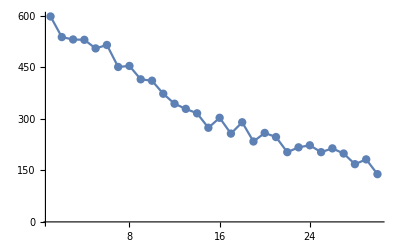
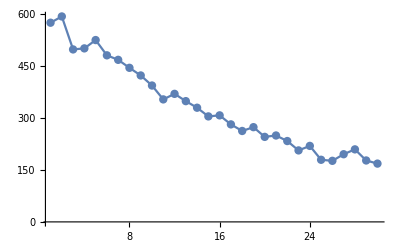
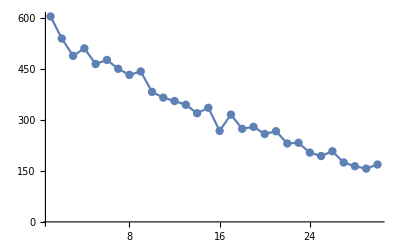

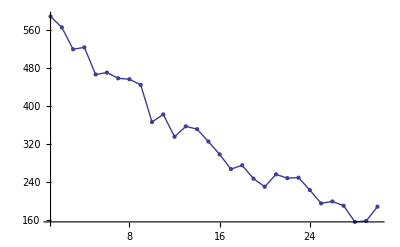
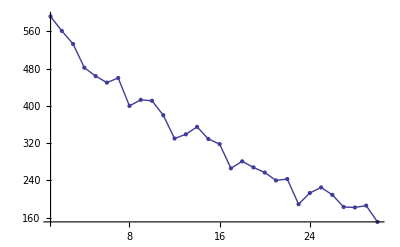
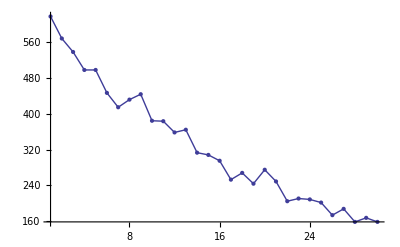

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

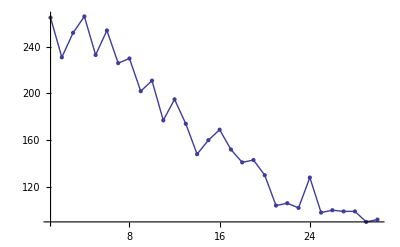
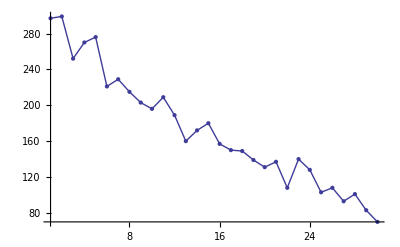
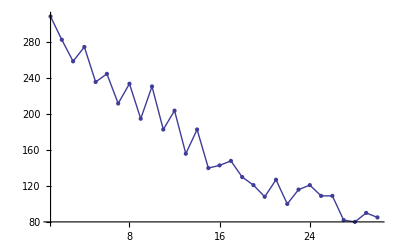
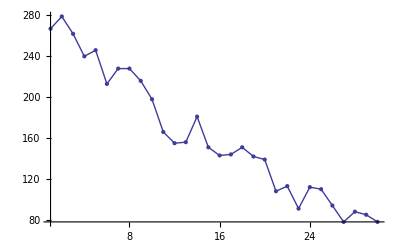
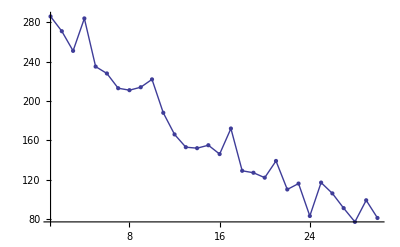

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[distanceCalculator2[0.04,365], PlotRange->All, Mesh-> All], {5}]
```

Scenarios (cf. StevenPinkersProblem.docx)

The plot below shows the total number of times strikes occur for each of the distances on the X axis. For example, for x = 10, each dot shows

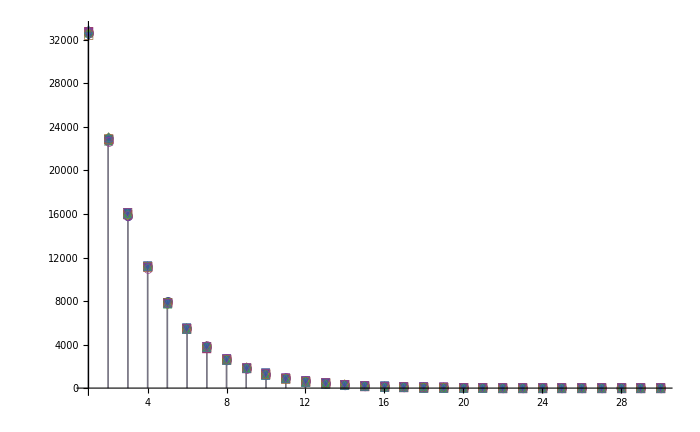

-Graphics-

```mathematica
ListPlot[Table[distanceCalculator2[0.3,365],{10}], PlotRange->All, Filling->Axis,PlotMarkers->{Automatic,12},ImageSize->700, LabelStyle->{12,Bold,FontFamily-> "Helvetica"}, AxesLabel->{"Distance Between Strikes", "Total # of Occurrences"}]
```

There is always a case in which the number of occurrences per trial for distance = 2 is greater that for distance 1.

Set::write: Tag Times in a always case for in is number occurrences of per the There which {30,47,1,95,18,5} {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,«315»} is Protected.

{60. for greater is that,94. for greater is that,2. for greater is that,190. for greater is that,36. for greater is that,10. for greater is that}

Distances for a single trial

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,a Distances for single,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,a Distances for single,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,a Distances for single,a Distances for single,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,a Distances for single,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,a Distances for single,0,0,0,0,a Distances for single,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

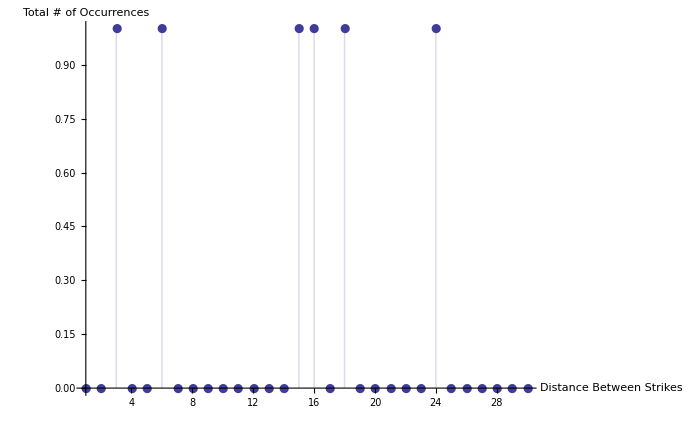

-Graphics-

```mathematica
ListPlot[(strikeDistance2[RandomChoice[{12/365, 353/365}->{1,0},365],#] & /@ Range[30]), PlotRange->All, Filling->Axis,PlotMarkers->{Automatic,12},ImageSize->700, LabelStyle->{12,Bold,FontFamily-> "Helvetica"}, AxesLabel->{"Distance Between Strikes", "# of Occurrences"}]
```

## Making it Dynamic

```mathematica
pinker = Manipulate[
(* Create the function for distance between strikes *)
strikeDistance2[trial_,dist_]:= Module[{pos,distances, d},
(* Distance between strikes in a trial is the distance between the 1s that occur in a trial. *)
pos = Flatten[Position[trial,1]];
(* Create 2-tuples of the pos values so that they can be subtracted to find the distance -- or the number of blanks -- between strikes. *)
distances = Partition[pos,2,1] /. {x_,y_} -> Subtract[y,x];
(* The number of instances where the distance = dist *)
d = Count[distances,dist]
];
(* Create a function for calculating and manipulating the occurences of strike distances as a function of the strike probability, the length of a single trial and the number of trials we conduct (which is defaulted to 500) *)
distanceCalculator2[probStrike_, trialLength_, nTrials_:100]:= Module[{probBlank, trial, setOfTrials, maxDistance,totalOccurrences, distOccurrencePerTrial, pdistOccurrencePerTrial},
probBlank = 1 - probStrike;
(* Generate the set of nTrials trials *)
setOfTrials = Table[RandomChoice[{probStrike, probBlank}->{1,0},trialLength],{nTrials}];
(* For each distance value, calculate the number of occurrences of that distance value in each trial. *)
(* Only the first few distances are relevant -- so save time and calculate only for those distances. *)
maxDistance = 30;
(* Total count of the occurrences of the distance in the set of trials *)
totalOccurrences = Table[Total@(strikeDistance2[#, i] & /@ setOfTrials), {i,1,maxDistance}];
distOccurrencePerTrial = Table[N[Total@(strikeDistance2[#, i] & /@ setOfTrials)/nTrials], {i,1,maxDistance}];
(* pdistOccurrencePerTrial = ListLinePlot[distOccurrencePerTrial] *)
totalOccurrences
];
ListPlot[Table[distanceCalculator2[pStrike,365],{3}], PlotLabel -> "Probability of Strike = " <> ToString[pStrike],PlotRange->All, Filling->Axis,PlotMarkers->{Automatic,12},ImageSize->700, LabelStyle->{12,Bold,FontFamily-> "Helvetica"}, AxesLabel->{"Distance Between Strikes", "Total # of Occurrences"}],
{{pStrike,0.03, "Probability of a Strike"}, {0.001, 0.01, 0.03, 0.1, 0.3, 0.5, 0.8}, Appearance->"Labeled"}]
```